# Prime Counting Function

### Author

Eric W. Weisstein
March 7, 2020

This notebook downloaded from http://mathworld.wolfram.com/notebooks/PrimeNumbers/PrimeCountingFunction.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/PrimeCountingFunction.html.

©2020 Wolfram Research, Inc. except for portions noted otherwise

### Code

```mathematica
OrderOfMag[n_,m_,a_List]:=Module[{i,b=a,start=10^(n-1)+1},
Do[
If[PrimeQ[i],b[[Mod[i,m]+1]]++],
{i,start,10^n}
];
b
]

R[x_]:=NSum[MoebiusMu[k]/k LogIntegral[x^(1/k)],{k,Infinity}]
```

## Plot

#### V5

```mathematica
<<Utilities`Plot`
```

```mathematica
IntegerListPlot[Table[PrimePi[n],{n,200}],PlotJoined->True,AxesLabel->TraditionalForm/@{n,PrimePi[n]},
PlotStyle->Red]
```

⁃Graphics⁃

#### V6

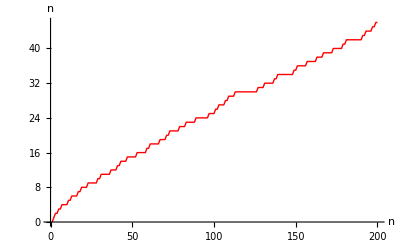

```mathematica
ListLinePlot[PrimePi[Range[200]],Joined->True,PlotStyle->Red,AxesLabel->{n,PrimePi[n]},ImageSize->400]
```

## Tables

### Edwards 2001, pp. 2–3

```mathematica
Integrate[1/Log[t],{t,2,n},Assumptions->n>2]
```

-LogIntegral[2]+LogIntegral[n]

```mathematica
Table[{n,p1=PrimePi[n],p2=N[LogIntegral[n],10],p2-p1},{n,5*^5,3*^6,5*^5}]//TableForm
```

500000 | 41538 | 41606.2888 | 68.28879
1000000 | 78498 | 78627.54916 | 129.5492
1500000 | 114155 | 114263.0897 | 108.09
2000000 | 148933 | 149054.8332 | 121.833
2500000 | 183072 | 183244.9892 | 172.989
3000000 | 216816 | 216970.564 | 154.564

## Counts

### Algorithms

Charles, Sep 17, 2018:

https://github.com/kimwalisch/primecount was used to produce the record PrimePi[10^27] with the Deleglise-Rivat method.

### Mathematica

#### V5.0.1

```mathematica
Table[PrimePi[10^n],{n,0,14}]//Timing
```

{147.81 Second,{0,4,25,168,1229,9592,78498,664579,5761455,50847534,455052511,4118054813,37607912018,346065536839,3204941750802}}

```mathematica
lo=1;
hi=10^22;
i=0;
While[hi>lo+1,
x=Floor[(lo+hi)/2];
If[TimeConstrained[PrimePi[x],.5]===$Aborted,lo=x,hi=x];
If[Mod[++i,10]==0,Print[{i,lo,hi}]];
];
Print[{i,lo,hi}]
```

PrimePi::largp: Argument 5000000000000000000000 in PrimePi[5000000000000000000000] is too large for this implementation. More…

PrimePi::largp: Argument 2500000000000000000000 in PrimePi[2500000000000000000000] is too large for this implementation. More…

PrimePi::largp: Argument 1250000000000000000000 in PrimePi[1250000000000000000000] is too large for this implementation. More…

General::stop: Further output of PrimePi :: "largp" will be suppressed during this calculation. More…

{10,1,9765625000000000000}

{20,1,9536743164062500}

{30,242143869400024,251457095146179}

{40,249992808676323,250001903623341}

{50,249999994039737,250000002921521}

{60,249999999998511,250000000007185}

{70,249999999999992,250000000000001}

{74,249999999999999,250000000000000}

```mathematica
hi//N//ScientificForm
```

2.5×10^14

```mathematica
PrimePi[hi]
```

PrimePi::largp: Argument 250000000000000 in PrimePi[250000000000000] is too large for this implementation. More…

PrimePi[250000000000000]

#### V6

```mathematica
Table[PrimePi[10^n],{n,0,14}]//Timing
```

{157.87 Second,{0,4,25,168,1229,9592,78498,664579,5761455,50847534,455052511,4118054813,37607912018,346065536839,3204941750802}}

```mathematica
PrimePi[10^15]//Timing
```

{1378. Second,29771634079304}

...wrong...

```mathematica
primepi[[15]]
```

29844570422669

#### V6.0.0 32-bit

```mathematica
lo=1;
hi=10^22;
i=0;
While[hi>lo+1,
x=Floor[(lo+hi)/2];
If[TimeConstrained[PrimePi[x],.5]===$Aborted,lo=x,hi=x];
If[Mod[++i,10]==0,Print[{i,lo,hi}]];
];
Print[{i,lo,hi}]
```

PrimePi::largp: Argument 5000000000000000000000 in PrimePi[5000000000000000000000] is too large for this implementation. More…

PrimePi::largp: Argument 2500000000000000000000 in PrimePi[2500000000000000000000] is too large for this implementation. More…

PrimePi::largp: Argument 1250000000000000000000 in PrimePi[1250000000000000000000] is too large for this implementation. More…

General::stop: Further output of PrimePi :: "largp" will be suppressed during this calculation. More…

{10,1,9765625000000000000}

{20,1,9536743164062500}

{30,242143869400024,251457095146179}

{40,249992808676323,250001903623341}

{50,249999994039737,250000002921521}

{60,249999999998511,250000000007185}

{70,249999999999992,250000000000001}

{74,249999999999999,250000000000000}

```mathematica
hi//N//ScientificForm
```

2.5×10^14

```mathematica
PrimePi[hi]
```

PrimePi::largp: Argument 250000000000000 in PrimePi[250000000000000] is too large for this implementation. More…

PrimePi[250000000000000]

```mathematica
TimeConstrained[PrimePi[hi-1],10]//Timing
```

{8.67 Second,$Aborted}

#### V6.0.1 64-bit

```mathematica
$Version
```

6.0 for Mac OS X x86 (64-bit) (June 19, 2007)

```mathematica
lo=1;
hi=10^22;
i=0;
While[hi>lo+1,
x=Floor[(lo+hi)/2];
If[TimeConstrained[PrimePi[x],.5]===$Aborted,lo=x,hi=x];
If[Mod[++i,10]==0,Print[{i,lo,hi}]];
];
Print[{i,lo,hi}]
```

PrimePi::largp: Argument 5000000000000000000000 in PrimePi[5000000000000000000000] is too large for this implementation.

PrimePi::largp: Argument 2500000000000000000000 in PrimePi[2500000000000000000000] is too large for this implementation.

PrimePi::largp: Argument 1250000000000000000000 in PrimePi[1250000000000000000000] is too large for this implementation.

General::stop: Further output of PrimePi :: "largp" will be suppressed during this calculation.

{10,1,9765625000000000000}

{20,1,9536743164062500}

{30,242143869400024,251457095146179}

{40,249992808676323,250001903623341}

{50,249999994039737,250000002921521}

{60,249999999998511,250000000007185}

{70,249999999999992,250000000000001}

{74,249999999999999,250000000000000}

#### V7

```mathematica
$Version
```

7.0 for Mac OS X x86 (64-bit) (December 2, 2008)

```mathematica
lo=1;
hi=10^22;
i=0;
While[hi>lo+1,
x=Floor[(lo+hi)/2];
If[TimeConstrained[PrimePi[x],.5]===$Aborted,lo=x,hi=x];
If[Mod[++i,10]==0,Print[{i,lo,hi}]];
];
Print[{i,lo,hi}]
```

{10,1,9765625000000000000}

{20,1,9536743164062500}

{30,242143869400024,251457095146179}

{40,249992808676323,250001903623341}

{50,249999994039737,250000002921521}

{60,249999999998511,250000000007185}

{70,249999999999992,250000000000001}

{74,249999999999999,250000000000000}

#### V12.1 Mac

```mathematica
$Version
```

12.1.0 for Mac OS X x86 (64-bit) (February 11, 2020)

```mathematica
Do[Print[{n,10^n,PrimePi[10^n]//Timing//AbsoluteTiming}],{n,20}]
```

{1,10,{0.000011,{8.×10^-6,4}}}

{2,100,{5.×10^-6,{3.×10^-6,25}}}

{3,1000,{0.001567,{0.001554,168}}}

{4,10000,{0.000151,{0.000149,1229}}}

{5,100000,{0.000137,{0.000135,9592}}}

{6,1000000,{3.×10^-6,{2.×10^-6,78498}}}

{7,10000000,{0.002508,{0.002502,664579}}}

{8,100000000,{0.003054,{0.00305,5761455}}}

{9,1000000000,{0.003663,{0.003659,50847534}}}

{10,10000000000,{0.071518,{0.073618,455052511}}}

{11,100000000000,{0.006652,{0.039788,4118054813}}}

{12,1000000000000,{0.016995,{0.101754,37607912018}}}

{13,10000000000000,{0.049635,{0.296163,346065536839}}}

{14,100000000000000,{0.183376,{1.09654,3204941750802}}}

{15,1000000000000000,{0.684829,{4.08921,29844570422669}}}

{16,10000000000000000,{2.76548,{16.5166,279238341033925}}}

{17,100000000000000000,{12.063,{72.0693,2623557157654233}}}

{18,1000000000000000000,{51.8619,{308.34,24739954287740860}}}

{19,10000000000000000000,{210.861,{1256.44,234057667276344607}}}

{20,100000000000000000000,{921.238,{5463.17,2220819602560918840}}}

```mathematica
counts={{1,10,{0.000011,{8.*^-6,4}}},{2,100,{5.*^-6,{3.*^-6,25}}},{3,1000,{0.001567,{0.001554,168}}},{4,10000,{0.000151,{0.000149,1229}}},{5,100000,{0.000137,{0.000135,9592}}},{6,1000000,{3.*^-6,{2.*^-6,78498}}},{7,10000000,{0.002508,{0.002502,664579}}},{8,100000000,{0.003054,{0.00305,5761455}}},{9,1000000000,{0.003663,{0.003659,50847534}}},{10,10000000000,{0.071518,{0.073618,455052511}}},{11,100000000000,{0.006652,{0.039788,4118054813}}},{12,1000000000000,{0.016995,{0.101754,37607912018}}},{13,10000000000000,{0.049635,{0.296163,346065536839}}},{14,100000000000000,{0.183376,{1.096537,3204941750802}}},{15,1000000000000000,{0.684829,{4.089214,29844570422669}}},{16,10000000000000000,{2.765478,{16.516597,279238341033925}}},{17,100000000000000000,{12.062986,{72.069293,2623557157654233}}},{18,1000000000000000000,{51.861935,{308.339925,24739954287740860}}},{19,10000000000000000000,{210.860767,{1256.440029,234057667276344607}}},{20,100000000000000000000,{921.237721,{5463.168828,2220819602560918840}}}}[[All,-1,-1,-1]]
```

{4,25,168,1229,9592,78498,664579,5761455,50847534,455052511,4118054813,37607912018,346065536839,3204941750802,29844570422669,279238341033925,2623557157654233,24739954287740860,234057667276344607,2220819602560918840}

```mathematica
Take[primepi,Length[counts]]==counts
```

True

#### V12.1 byblis67

```mathematica
$Version
```

12.2.0 for Linux x86 (64-bit) (February 24, 2020)

```mathematica
Do[Print[{n,PrimePi[10^n]//Timing//AbsoluteTiming}],{n,20}]
```

{1,{0.000029,{0.000021,4}}}

{2,{0.00001,{6.×10^-6,25}}}

{3,{0.000481,{0.000489,168}}}

{4,{0.000474,{0.000521,1229}}}

{5,{0.000427,{0.000472,9592}}}

{6,{9.×10^-6,{4.×10^-6,78498}}}

{7,{0.003221,{0.00323,664579}}}

{8,{0.003966,{0.004012,5761455}}}

{9,{0.004953,{0.004999,50847534}}}

{10,{0.002713,{0.011006,455052511}}}

{11,{0.008012,{0.080865,4118054813}}}

{12,{0.020748,{0.227232,37607912018}}}

{13,{0.081245,{0.891262,346065536839}}}

{14,{0.198534,{2.17933,3204941750802}}}

{15,{0.816602,{8.54474,29844570422669}}}

{16,{2.93159,{26.8306,279238341033925}}}

{17,{10.451,{99.0088,2623557157654233}}}

{18,{47.9624,{406.745,24739954287740860}}}

{19,{212.011,{2046.22,234057667276344607}}}

{20,{890.467,{9384.27,2220819602560918840}}}

{21,{4094.77,{41410.6,21127269486018731928}}}

{22,{23274.6,{206811.,201467286689315906290}}}

{23,{106137.,{977100.,1925320391606803968923}}}

```mathematica
data=Flatten/@{{1,{0.000029,{0.000021,4}}},{2,{0.00001,{6.*^-6,25}}},{3,{0.000481,{0.000489,168}}},{4,{0.000474,{0.000521,1229}}},{5,{0.000427,{0.000472,9592}}},{6,{9.*^-6,{4.*^-6,78498}}},{7,{0.003221,{0.00323,664579}}},{8,{0.003966,{0.004012,5761455}}},{9,{0.004953,{0.004999,50847534}}},{10,{0.002713,{0.011006,455052511}}},{11,{0.008012,{0.080865,4118054813}}},{12,{0.020748,{0.227232,37607912018}}},{13,{0.081245,{0.891262,346065536839}}},{14,{0.198534,{2.179332,3204941750802}}},{15,{0.816602,{8.544741,29844570422669}}},{16,{2.931589,{26.830573,279238341033925}}},{17,{10.45102,{99.008838,2623557157654233}}},{18,{47.962359,{406.745247,24739954287740860}}},{19,{212.011162,{2046.216741,234057667276344607}}},{20,{890.467344,{9384.273426,2220819602560918840}}},{21,{4094.767588,{41410.609275,21127269486018731928}}},{22,{23274.634755,{206810.631538,201467286689315906290}}},{23,{106136.727294,{977099.735884,1925320391606803968923}}},{24,{362482.,{4.33635*^6,18435599767349200867866}}}};
```

```mathematica
TextGrid[data,Dividers->All,Alignment->Decimal]
```

1 | 0.000029 | 0.000021 | 4
2 | 0.00001 | 6.×10^-6 | 25
3 | 0.000481 | 0.000489 | 168
4 | 0.000474 | 0.000521 | 1229
5 | 0.000427 | 0.000472 | 9592
6 | 9.×10^-6 | 4.×10^-6 | 78498
7 | 0.003221 | 0.00323 | 664579
8 | 0.003966 | 0.004012 | 5761455
9 | 0.004953 | 0.004999 | 50847534
10 | 0.002713 | 0.011006 | 455052511
11 | 0.008012 | 0.080865 | 4118054813
12 | 0.020748 | 0.227232 | 37607912018
13 | 0.081245 | 0.891262 | 346065536839
14 | 0.198534 | 2.17933 | 3204941750802
15 | 0.816602 | 8.54474 | 29844570422669
16 | 2.93159 | 26.8306 | 279238341033925
17 | 10.451 | 99.0088 | 2623557157654233
18 | 47.9624 | 406.745 | 24739954287740860
19 | 212.011 | 2046.22 | 234057667276344607
20 | 890.467 | 9384.27 | 2220819602560918840
21 | 4094.77 | 41410.6 | 21127269486018731928
22 | 23274.6 | 206811. | 201467286689315906290
23 | 106137. | 977100. | 1925320391606803968923
24 | 362482. | 4.33635×10^6 | 18435599767349200867866

```mathematica
TextGrid[{#1,Quantity[#2,"Seconds"],Quantity[#3,"Seconds"],#4}&@@@data/.q_Quantity:>UnitConvert[q,MixedUnit[{"Days","Hours"}]],Dividers->All,Alignment->Decimal]
```

1 | 0 8.05556×10^-9 | 0 5.83333×10^-9 | 4
2 | 0 2.77778×10^-9 | 0 1.66667×10^-9 | 25
3 | 0 1.33611×10^-7 | 0 1.35833×10^-7 | 168
4 | 0 1.31667×10^-7 | 0 1.44722×10^-7 | 1229
5 | 0 1.18611×10^-7 | 0 1.31111×10^-7 | 9592
6 | 0 2.5×10^-9 | 0 1.11111×10^-9 | 78498
7 | 0 8.94722×10^-7 | 0 8.97222×10^-7 | 664579
8 | 0 1.10167×10^-6 | 0 1.11444×10^-6 | 5761455
9 | 0 1.37583×10^-6 | 0 1.38861×10^-6 | 50847534
10 | 0 7.53611×10^-7 | 0 3.05722×10^-6 | 455052511
11 | 0 2.22556×10^-6 | 0 0.0000224625 | 4118054813
12 | 0 5.76333×10^-6 | 0 0.00006312 | 37607912018
13 | 0 0.0000225681 | 0 0.000247573 | 346065536839
14 | 0 0.0000551483 | 0 0.00060537 | 3204941750802
15 | 0 0.000226834 | 0 0.00237354 | 29844570422669
16 | 0 0.00081433 | 0 0.00745294 | 279238341033925
17 | 0 0.00290306 | 0 0.0275025 | 2623557157654233
18 | 0 0.0133229 | 0 0.112985 | 24739954287740860
19 | 0 0.058892 | 0 0.568394 | 234057667276344607
20 | 0 0.247352 | 0 2.60674 | 2220819602560918840
21 | 0 1.13744 | 0 11.5029 | 21127269486018731928
22 | 0 6.46518 | 2 9.4474 | 201467286689315906290
23 | 1 5.48242 | 11 7.41659 | 1925320391606803968923
24 | 4 4.68944 | 50 4.54167 | 18435599767349200867866

```mathematica
counts=data[[All,-1]]
```

{4,25,168,1229,9592,78498,664579,5761455,50847534,455052511,4118054813,37607912018,346065536839,3204941750802,29844570422669,279238341033925,2623557157654233,24739954287740860,234057667276344607,2220819602560918840,21127269486018731928,201467286689315906290,1925320391606803968923,18435599767349200867866}

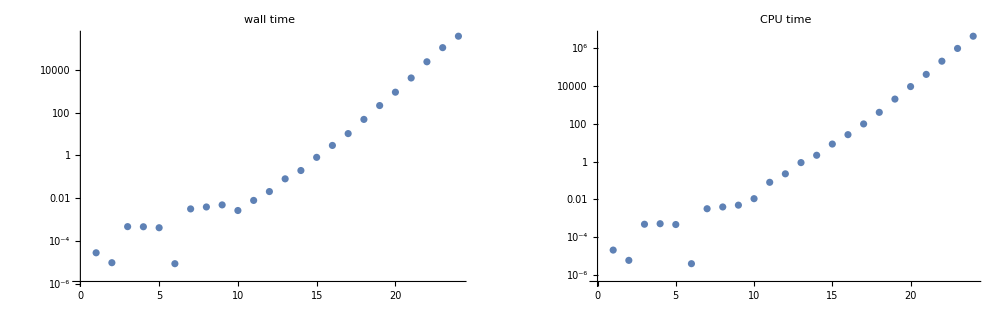

```mathematica
GraphicsRow[{ListLogPlot[data[[All,2]],PlotLabel->"wall time"],ListLogPlot[data[[All,3]],PlotLabel->"CPU time"]},ImageSize->1000]
```

### Estimated based on 1-23

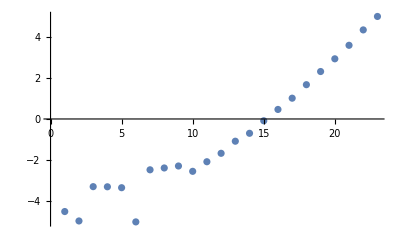

```mathematica
plot1=ListPlot[{#,Log10[#2]}&@@@data[[All,;;2]]]
```

```mathematica
fit=FindFit[{#1,Log10[#2]}&@@@Drop[data[[All,;;2]],10],model=a x^2+b x+c ,{a,b,c},x]
```

{a→0.0115907,b→0.203662,c→-5.75974}

```mathematica
line=model/.fit
```

-5.75974+0.203662 x+0.0115907 x^2

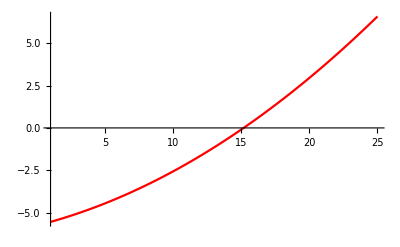

```mathematica
plot2=Plot[line,{x,1,25},PlotStyle->Red]
```

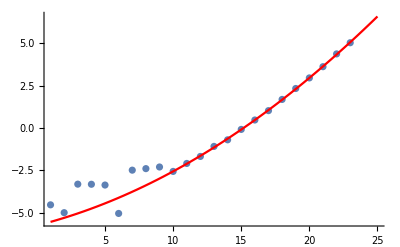

```mathematica
Show[{plot1,plot2},PlotRange->All]
```

Estimated number of wall clock days to compute:

```mathematica
Table[10^(line/.x->n)/86400.,{n,24,25}]
```

{7.37709,43.6006}

### Estimated based on 1-24

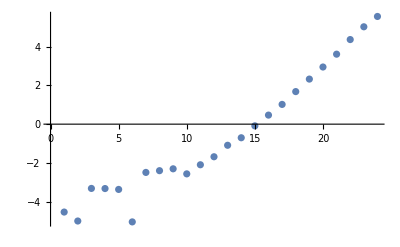

```mathematica
plot1=ListPlot[{#,Log10[#2]}&@@@data[[All,;;2]]]
```

```mathematica
fit=FindFit[{#1,Log10[#2]}&@@@Drop[data[[All,;;2]],10],model=a x^2+b x+c ,{a,b,c},x]
```

{a→0.00940222,b→0.273256,c→-6.28936}

```mathematica
line=model/.fit
```

-6.28936+0.273256 x+0.00940222 x^2

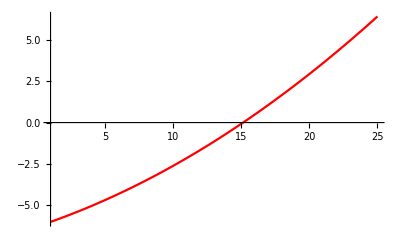

```mathematica
plot2=Plot[line,{x,1,25},PlotStyle->Red]
```

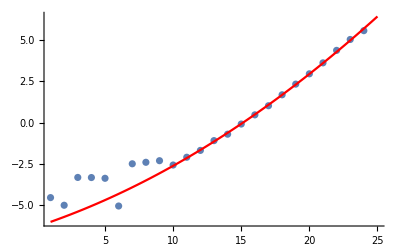

```mathematica
Show[{plot1,plot2},PlotRange->All]
```

Estimated number of wall clock days to compute:

```mathematica
Table[10^(line/.x->n)/86400.,{n,24,26}]
```

{5.597,30.3333,171.668}

### OEIS

A006880

```mathematica
primepi={4,25,168,1229,9592,78498,664579,5761455,50847534,455052511,4118054813,37607912018,346065536839,3204941750802,29844570422669,279238341033925,2623557157654233,24739954287740860,234057667276344607,2220819602560918840,21127269486018731928,201467286689315906290,1925320391606803968923,18435599767349200867866,176846309399143769411680,1699246750872437141327603,16352460426841680446427399};
```

```mathematica
Length[primepi]
```

27

```mathematica
Position[counts-Take[primepi,Length[counts]],Except[_Integer,0]]
```

{}

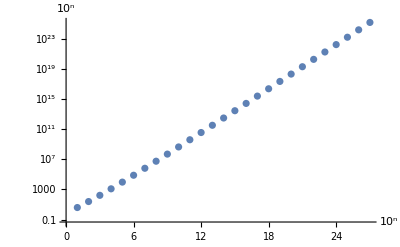

```mathematica
ListLogPlot[primepi,AxesLabel->{10^n,PrimePi[10^n]}]
```

## f(x)

### f_1

```mathematica
PrimePowersLessThanEqual[x_]:=Sort[Flatten[Table[{p,n},{p,Prime[Range[PrimePi[x]]]},{n,Log[p,x]}],1]]
```

```mathematica
Table[PrimePowersLessThanEqual[n],{n,10}]//Column
```

{}
{{2,1}}
{{2,1},{3,1}}
{{2,1},{2,2},{3,1}}
{{2,1},{2,2},{3,1},{5,1}}
{{2,1},{2,2},{3,1},{5,1}}
{{2,1},{2,2},{3,1},{5,1},{7,1}}
{{2,1},{2,2},{2,3},{3,1},{5,1},{7,1}}
{{2,1},{2,2},{2,3},{3,1},{3,2},{5,1},{7,1}}
{{2,1},{2,2},{2,3},{3,1},{3,2},{5,1},{7,1}}

```mathematica
f1[x_]:=Total[1/PrimePowersLessThanEqual[x][[All,2]]]
```

```mathematica
Array[f1,10]
```

{0,1,2,5/2,7/2,7/2,9/2,29/6,16/3,16/3}

### f_2

```mathematica
f21[x_]:=Sum[If[PrimePowerQ[k],1/FactorInteger[k][[1,2]],0],{k,2,x}]
```

```mathematica
Array[f21,10]
```

{0,1,2,5/2,7/2,7/2,9/2,29/6,16/3,16/3}

```mathematica
f22[x_]:=Sum[Boole[PrimePowerQ[k]]/FactorInteger[k][[1,2]],{k,2,x}]
```

```mathematica
Array[f22,10]
```

{0,1,2,5/2,7/2,7/2,9/2,29/6,16/3,16/3}

```mathematica
f23[x_]:=Sum[If[Length[fac=FactorInteger[k]]==1,1/fac[[1,2]],0],{k,2,x}]
```

```mathematica
Array[f23,10]
```

{0,1,2,5/2,7/2,7/2,9/2,29/6,16/3,16/3}

### f_3

```mathematica
Sum[PrimePi[x^(1/k)]/k,{k,Log2[x]}]
```

∑_k^(Log[x]/Log[2]) PrimePi[x^(1/k)]/k

```mathematica
f3[x_]:=Sum[PrimePi[x^(1/k)]/k,{k,Log2[x]}]
```

```mathematica
Array[f3,10]
```

{0,1,2,5/2,7/2,7/2,9/2,29/6,16/3,16/3}

### Compare

```mathematica
f1[100]==f2[100]==f3[100]
```

True

### Plot

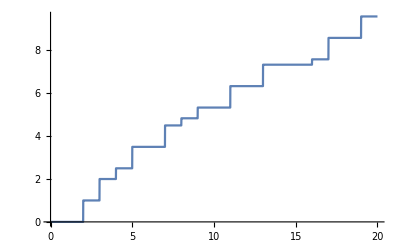

```mathematica
Plot[f2[x],{x,0,20}]
```

## Differences from estimators

### Locker-Ernst

```mathematica
Select[Table[{n,N[PrimePi[n]-n/(HarmonicNumber[n]-3/2)]},{n,1000,5000}],#[[2]]≤0&]
```

{{1007,-0.044986},{1008,-0.18402},{1397,-0.0563398},{1398,-0.18954},{1405,-0.121602},{1406,-0.254705},{1407,-0.387795},{1408,-0.520874},{1412,-0.0530669},{1413,-0.186085},{1414,-0.319091},{1415,-0.452085},{1416,-0.585066},{1417,-0.718036},{1418,-0.850994},{1419,-0.983939},{1420,-1.11687},{1421,-1.24979},{1422,-1.3827},{1423,-0.515602},{1424,-0.648488},{1425,-0.781361},{1426,-0.914223},{1427,-0.0470728},{1428,-0.179911}}

```mathematica
Show[GraphicsArray[{
ListPlot[Table[{n,N[PrimePi[n]-n/(HarmonicNumber[n]-3/2)]},{n,50,1000}],Joined->True,AxesLabel->{n,PrimePi[n]-n/Subscript[h, n]}],
ListPlot[Table[{n,N[PrimePi[n]-n/(HarmonicNumber[n]-3/2)]},{n,50,10000,10}],Joined->True,AxesLabel->{n,PrimePi[n]-n/Subscript[h, n]}]
}]]
```

⁃GraphicsArray⁃

### R(x), li(x)

```mathematica
Show[GraphicsArray[{
ListPlot[Table[R[x]-PrimePi[x],{x,2,1000}],Joined->True,AxesLabel->{x,HoldForm[R[x]]-PrimePi[x]}],
ListPlot[Table[LogIntegral[x]-PrimePi[x],{x,2,1000}],Joined->True,AxesLabel->{x,LogIntegral[x]-PrimePi[x]}]
}]]
```

⁃GraphicsArray⁃

## Formulas

### n==∑_(j=3)^n ((j-2)!-j Floor[((j-2)!)/j])-1

Whittaker and Watson

```mathematica
primePi[n_]:=-1+Sum[(j-2)!-j Floor[(j-2)!/j],{j,3,n}]
```

```mathematica
Table[PrimePi[n]-primePi[n],{n,200}]
```

{1,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
-1+Sum[(j-2)!-j Floor[((j-2)!)/j],{j,3,n}]
```

-1 + Sum[(-2 + j)! - j*Floor[(-2 + j)!/j], {j, 3, n}]

```mathematica
l1=Table[-1+Sum[(j-2)!-j Floor[((j-2)!)/j],{j,3,n}],{n,50}]
```

{-1,-1,0,2,3,3,4,4,4,4,5,5,6,6,6,6,7,7,8,8,8,8,9,9,9,9,9,9,10,10,11,11,11,11,11,11,12,12,12,12,13,13,14,14,14,14,15,15,15,15}

```mathematica
l2=PrimePi[Range[50]]
```

{0,1,2,2,3,3,4,4,4,4,5,5,6,6,6,6,7,7,8,8,8,8,9,9,9,9,9,9,10,10,11,11,11,11,11,11,12,12,12,12,13,13,14,14,14,14,15,15,15,15}

```mathematica
l1-l2
```

{-1,-2,-2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

## Inequalities

### (π(x))^2<(e x)/lnx π(x/e)

```mathematica
l=1+Position[Table[PrimePi[x]^2<(E x)/Log[x] PrimePi[x/E],{x,2,100}],True]//Flatten
```

{6,9,10,12,14,15,16,18,20,21,22,24,25,26,27,28,30,31,32,33,34,35,36,37,38,39,40,41,42,47,48,49,50,51,52,53,54,55,56,57,58,59,60,62,63,64,65,66,67,68,69,70,71,72,79,80,81,82,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

```mathematica
Function[x,PrimePi[x]^2<(E x)/Log[x] PrimePi[x/E]]/@l//Union
```

{True}

```mathematica
PrimePi[x]^2<(E x)/Log[x] PrimePi[x/E]/.x->38358837677//Timing
```

{1.26 Second,False}

```mathematica
PrimeQ[38358837677]
```

True

```mathematica
PrimePi[38358837677]
```

1644673232

```mathematica
Function[x,PrimePi[x]^2<(E x)/Log[x] PrimePi[x/E]]/@Table[Prime[1644673232+n],{n,0,10}]
```

{False,True,True,True,True,True,True,True,True,True,True}

### (Li(x))^2<(e x)/lnx Li(x/e)

```mathematica
Li[x_]:=LogIntegral[x]-LogIntegral[2]
```

```mathematica
1+Position[Table[Li[x]^2<(E x)/Log[x] Li[x/E],{x,2,5000}],True]//Flatten//Timing
```

{19.75 Second,{}}

```mathematica
li[x_]:=LogIntegral[x]
```

```mathematica
1+Position[Table[li[x]^2<(E x)/Log[x] li[x/E],{x,2,2500}],True]//Flatten//Timing
```

{9.23 Second,{2418,2419,2420,2421,2422,2423,2424,2425,2426,2427,2428,2429,2430,2431,2432,2433,2434,2435,2436,2437,2438,2439,2440,2441,2442,2443,2444,2445,2446,2447,2448,2449,2450,2451,2452,2453,2454,2455,2456,2457,2458,2459,2460,2461,2462,2463,2464,2465,2466,2467,2468,2469,2470,2471,2472,2473,2474,2475,2476,2477,2478,2479,2480,2481,2482,2483,2484,2485,2486,2487,2488,2489,2490,2491,2492,2493,2494,2495,2496,2497,2498,2499,2500}}